再谈纯函数

我们已经看到如何使用 Table 来创建列表和数组。还有一种方法是用纯函数 — 通过 Array。

用一个抽象函数 f 来生成一个包含 10 个元素的数组：

```mathematica
Array[f,10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

使用纯函数生成前 10 个数字的平方的列表：

```mathematica
Array[#^2&,10]
```

{1,4,9,16,25,36,49,64,81,100}

Table 可以得到同样的结果，但是你必须引入变量 n：

```mathematica
Table[n^2,{n,10}]
```

{1,4,9,16,25,36,49,64,81,100}

Array[f,4] 将创建一个包含 4 个元素的列表。 Array[f,{3,4}] 将生成一个 3×4 的数组。

创建一个长度为 3 的列表，其每个元素都是长度为 4 的列表：

```mathematica
Array[f,{3,4}]
```

{{f[1,1],f[1,2],f[1,3],f[1,4]},{f[2,1],f[2,2],f[2,3],f[2,4]},{f[3,1],f[3,2],f[3,3],f[3,4]}}

将它以网格形式显示：

```mathematica
Array[f,{3,4}]//Grid
```

f[1,1] | f[1,2] | f[1,3] | f[1,4]
f[2,1] | f[2,2] | f[2,3] | f[2,4]
f[3,1] | f[3,2] | f[3,3] | f[3,4]

如果函数是 Times，Array 将会创建出一个乘法表：

```mathematica
Grid[Array[Times,{5,5}]]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

如果我们想用一个纯函数来代替 Times 怎么办？当我们计算 Times[3,4] 时，我们会说 Times 被应用于两个参数。(在 Times[3,4,5] 中，Times 被应用于三个参数，等等。)在一个纯函数中，#1 代表第一个参数，#2 代表第二个参数，以此类推。

#1 代表第一个参数， #2 代表第二个参数：

```mathematica
f[#1,#2]&[55,66]
```

f[55,66]

#1 总是挑出第一个参数，而 #2 则挑出第二个参数：

```mathematica
f[#2,#1,{#2,#2,#1}]&[55,66]
```

f[66,55,{66,66,55}]

现在我们可以在 Array 中的函数使用 #1 和 #2 了：

使用纯函数来创建乘法表：

```mathematica
Array[#1*#2&,{5,5}]//Grid
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

使用另一个纯函数，只要数字相等就将 x 放进去：

```mathematica
Array[If[#1==#2,x,#1*#2]&,{5,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

下面是使用 Table 进行的等效计算：

```mathematica
Table[If[i==j,x,i*j],{i,5},{j,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

现在我们已经讨论了具有多个参数的纯函数，我们可以讨论 FoldList 了。你可以把 FoldList 看作是 NestList 推广到了两个参数。

NestList 接受一个函数，比如说 f，并依次对其进行嵌套：

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

当我们使用的函数是 Framed 时，它就很容易理解：

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

NestList 只是不断地将一个函数应用于它之前得到的任何结果。FoldList 也是如此，只是它每次都会“合并”一个新元素。

这里是使用抽象函数 f 的 FoldList：

```mathematica
FoldList[f,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

将 Framed 包含进去，可以让人更容易看清发生了什么：

```mathematica
FoldList[Framed[f[#1,#2]]&,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

刚开始时，这可能看起来很复杂和晦涩，而且似乎很难想象它怎么会有用。但实际上，它非常有用，而且在真正的程序中出奇地常见。

FoldList 适合用于逐步累加对象。让我们从一个简单的案例开始：逐步累加数字。

在每一步， FoldList 都会引入另一个元素(#2)，并将其加入到迄今为止的结果(#1)中：

```mathematica
FoldList[#1+#2&,0,{1,1,1,2,0,0}]
```

{0,1,2,3,5,5,5}

这是它正在进行的计算：

```mathematica
{0,0+1,(0+1)+1,((0+1)+1)+1,(((0+1)+1)+1)+2,((((0+1)+1)+1)+2)+0,(((((0+1)+1)+1)+2)+0)+0}
```

{0,1,2,3,5,5,5}

或者等同于：

```mathematica
{0,0+1,0+1+1,0+1+1+1,0+1+1+1+2,0+1+1+1+2+0,0+1+1+1+2+0+0}
```

{0,1,2,3,5,5,5}

使用符号可能更容易看清发生了什么：

```mathematica
FoldList[#1+#2&,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

当然，这种情况很简单，你实际上不需要一个纯函数：

```mathematica
FoldList[Plus,0,{a,b,c,d,e}]
```

{0,a,a+b,a+b+c,a+b+c+d,a+b+c+d+e}

FoldList 的一个经典用法是连续“合并”数字，然后从其数字列表中重建一个数字。

使用数字位连续构建数字，从第一个数字位开始：

```mathematica
FoldList[10#1+#2&,{8,7,6,1,2,3,9,8,7}]
```

{8,87,876,8761,87612,876123,8761239,87612398,876123987}

最后，让我们使用 FoldList 来从一个列表中合并连续的图像，在每个点上用 ImageAdd 将它们添加到迄今获得的图像中。

逐步合并列表中的图像，将它们与 ImageAdd 相结合：

```mathematica
FoldList[ImageAdd,
{ -Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics- }]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

FoldList 的概念起初并不是很容易理解的。但当你掌握了它，你就学会了一种极其强大的函数式编程技术，它是 Wolfram 语言中优雅抽象的典范。

词汇

Array[f,n] |   | 通过应用函数来创建数组
Array[f,{m,n}] |   | 创建 2D 数组
FoldList[f,x,list] |   | 连续应用函数，合并列表中的元素

"共有 6 道习题"
"以及 1 道附加题" | "开始练习 »"

使用 Prime 和 Array 来生成一个前 100 个质数的列表。»

| 期望输出： |  
  | {2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541} |

使用 Prime 和 Array 来计算前 100 个连续质数之间的差值。Use Prime and Array to find successive differences between the first 100 primes. »

| 期望输出： |  
  | {1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18} |

使用 Array 和 Grid 来创建一个 10 × 10 的加法表。»

| 期望输出： |  
  | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 |

使用 FoldList、Times 和 Range 来对 10 以内的数字连续相乘(阶乘)。»

| 期望输出： |  
  | {1,1,2,6,24,120,720,5040,40320,362880,3628800} |

使用 FoldList 和 Array 来计算前 10 个素数的连续乘积。»

| 期望输出： |  
  | {1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230} |

使用 FoldList 依次对 3 至 8 条边、不透明度为 0.2 的正多边形进行 ImageAdd。»

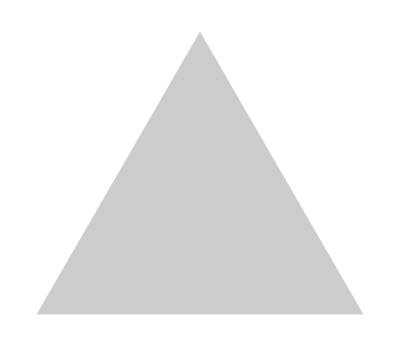
| 期望输出： |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

使用 Array 来创建一个 10 × 10 的网格，其中主对角线和下面的所有数值都为 1，其余都为 0。»

| 期望输出： |  
  | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |

问&答

单独的 # 是什么意思？

它等同于 #1 — 一个要使用函数的第一个参数填充的槽。

如何读 #1 呢？

可以是“slot 1”(反映它在纯函数中的作用)，或者“hash 1”(反映它的写法 — “#”通常被称为“hash”)。

可以给纯函数的参数命名吗？

是的，可以使用 Function[{x,y},x+y] 等来完成。为了代码的可读性，有时这样做是很好的，当嵌套纯函数时，有时也是必要的。

Array 可以创建更深的嵌套结构吗？

可以 — 你想多深都可以。列表的列表的列表 ... 任意级别的数量。

什么是函数式编程？

这是一种一切都基于对函数和函数组合的计算的编程。这实际上是我们在本书中迄今为止看到的唯一一种编程风格。在第38节中，我们将看到程序化编程，它是通过一个程序来逐步改变变量的值。

技术笔记

Fold 将给出 FoldList 的最后一个元素，就像 Nest 给出 NestList 的最后一个元素一样。

FromDigits 使用数字列表来重新构建数字，有效地完成了我们在上面使用 FoldList 来完成的工作。

Accumulate[list] 就是 FoldList[Plus,list]。

Array 和 FoldList，像 NestList 一样，是所谓的高阶函数的例子，它们将函数作为输入。(在数学上，它们也被称为泛函或函子。)

你可以用 # # 等来设置一次接受任意数量参数的纯函数。

你可以使用 ListAnimate 对图片列表进行动画处理，并使用 Image3D 对图片进行三维叠加显示。

探索更多

Wolfram 语言中函数式编程指南 »